### Нечеткие нейроны

```mathematica
f[x_,c_]:=Exp[-(x-c)^2];
f3[x_,a_,b_, c_]:=Min[1,Max[0,c+(b-Abs[x-a])/b]];
```

```mathematica
AndNeuron[x1_,x2_,w1_,w2_]:=Min[Max[w1,x1],Max[w2,x2]];
OrNeuron[x1_,x2_,w1_,w2_]:=Max[Min[w1,x1],Min[w2,x2]];
NotNeuron[x_]:=1-x;
(*Мамдани*)
ImplNeuron[x1_,x2_]:=Min[x1,x2];  
(*Клини-Даенса*)
ImplNeuron1[x1_,x2_]:=Max[1-x1,x2]; 
(*Лукасевича*)
ImplNeuron2[x1_,x2_]:=Min[1,1-x1+x2]; 
(*Ларсена*)
ImplNeuron3[x1_,x2_]:=x1*x2;
```

#### Нечеткий "И" нейрон

```mathematica
xmax=4;
Manipulate[
Plot[
{
f[x,-1],f[x,1],
AndNeuron[f[x,-1],f[x,1],w1,w2]
},
{x,-xmax,xmax}, 
PlotLegends->"Expressions",
Filling->{3->Axis}
],
{w1,0,1,0.05},
{w2,0,1,0.05}
]
```

#### Нечеткий "ИЛИ" нейрон

```mathematica
Manipulate[
Plot[
{
f[x,-1],f[x,1],
OrNeuron[f[x,-1],f[x,1],w1,w2]
},
{x,-xmax,xmax}, 
PlotLegends->"Expressions",
Filling->{3->Axis}
],
{w1,0,1,0.05},
{w2,0,1,0.05}
]
```

Plot::plln: Limiting value -xmax in {x,-xmax,xmax} is not a machine-sized real number.

#### Нечеткий "НЕ" нейрон

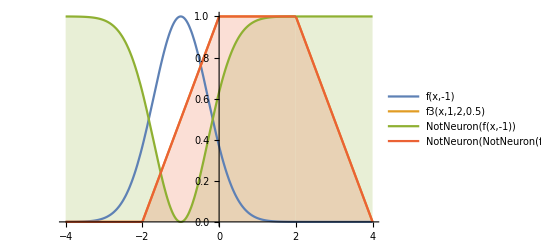

```mathematica
Plot[
{
f[x,-1],
f3[x,1,2,0.5],
NotNeuron[f[x,-1]],
NotNeuron[NotNeuron[f3[x,1,2,0.5]]]
},
{x,-xmax,xmax}, 
PlotLegends->"Expressions",
Filling->{3->Axis,4->Axis}
]
```

#### Нейрон "Импликация"

```mathematica
Manipulate[
{Plot[
{f[x,c1],f[x,c2],ImplNeuron[f[x,c1],f[x,c2]]},
{x,-xmax,xmax}, 
PlotLegends->"Expressions",
Filling->{3->Axis}
],
Plot[
{f[x,c1],f[x,c2],ImplNeuron3[f[x,c1],f[x,c2]]},
{x,-xmax,xmax}, 
PlotLegends->"Expressions",
Filling->{3->Axis}
]
},
{c1,-2,2,0.05},
{c2,-2,2,0.05}
]
```

```mathematica
Manipulate[
Plot[
{
f[x,c1],f[x,c2],
NotNeuron[ImplNeuron1[f[x,c1],f[x,c2]]],
(*ImplNeuron1[f[x,c1],f[x,c2]]*)
},
{x,-xmax,xmax}, 
PlotLegends->"Expressions",
Filling->{3->Axis}
],
{c1,-1,1,0.05},
{c2,-1,1,0.05}
]
```

### Нечеткий вывод

```mathematica
Tn[x_,y_]:=Min[x,y];
Sn[x_,y_]:=Max[x,y];
A1[x_,w_]:=f[x,w];
A2[x_,w_]:=f[x,w];
B1[x_,w_]:=f[x,w];
B2[x_,w_]:=f[x,w];

Net1[x_,y_,w11_,w12_,w13_,w14_, w21_, w22_,w23_,w24_]:=
NotNeuron[
Sn[
Tn[
w21*A1[x,w11],
w22*B1[y,w13]],
Tn[
w23*A2[x,w12],
w24*B2[y,w14]]
]
];
```

```mathematica
net1=Net1[x,y,w11,w12,w13,w14, w21, w22,w23,w24];
Manipulate[
{
Plot3D[{Net1[x,y,w11,w12,w13,w14, w21, w22,w23,w24],alpha},{x,-xmax,xmax}, {y,-xmax,xmax} ],
RegionPlot[Net1[x,y,w11,w12,w13,w14, w21, w22,w23,w24]>alpha,{x,-xmax,xmax}, {y,-xmax,xmax}]
},
{w11,-1,1,0.05},
{w12,-1,1,0.05},
{w13,-1,1,0.05},
{w14,-1,1,0.05},
{w21,-1,1,0.05},
{w22,-1,1,0.05},
{w23,-1,1,0.05},
{w24,-1,1,0.05},
{alpha,0,2,0.05}
]
```